# Calibration Script

This notebook has the paper equations coded and is used to find the unknown parameters μ, w, B_I and β by calibrating the model equations to data.

## Import Packages

```mathematica
Needs["NumericalDifferentialEquationAnalysis`"]
```

## Declare Equations

The equations are often defined in multiple ways often but not necessarily including 1. a version normalized by the storage, 2. a version that is not normalized, and 3. a version using Legendre Quadrature in cases where numerical integration is required.

```mathematica
(*Soil Moisture PDF based on Numerical estimation of the normalization constant*)
Clear[pz,pzm,χPDF,χIavgN1,aλ,aPET, pzm, pz,pqm,PQm,σ2Qm,aλ,pχ,CC1N,ϑ,pqmIntegrand,C1NFast,σ2QmFast,χavgFast,PQmFast,quadratureData]

(*Rainfall PDF, exponential and mixed exponential*)
pz[z_,γ_]:=γ ⅇ^(-γ z)UnitStep[z]
pzm[z_,ω_,γo_,γs_]:=(ω γo ⅇ^(-γo z)+(1-ω)γs ⅇ^(-γs z))UnitStep[z]
(*Soil Moisture (zero) top layer PDF *)
(*N1[DI_?NumericQ,γ_?NumericQ]:=N1[DI,γ]=1/NIntegrate[ⅇ^(-γ x0)x0^(γ/DI-1),{x0,0,1},AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]*)
χPDF[x0_?NumericQ,DI_?NumericQ,γ_?NumericQ]:=χPDF[x0,DI,γ]=(γ^(γ/DI)/Gamma[γ/DI,0,γ]) ⅇ^(-γ x0)x0^(γ/DI-1)(*UnitStep[1-x0]UnitStep[x0]*)
χIavg[DI_?NumericQ,γ_?NumericQ]:=χIavg[DI,γ]= (1/DI-(γ^(γ/DI-1)ⅇ^-γ)/Gamma[γ/DI,0,γ])

(*Average based on the numerical PDF*)(*DI=(γ k)/λ*)
(*χIavgN[DI_?NumericQ,γ_?NumericQ]:=χIavgN[DI,γ]=NIntegrate[x0 χPDF[x0,DI,γ],{x0,0,1},AccuracyGoal->3,Method->{Automatic,"SymbolicProcessing"->0}]*)

χIavgN1[DI_?NumericQ,γ_?NumericQ]:=χIavgN1[DI,γ]=UnitStep[χIavg[DI,γ]-1]+UnitStep[1-χIavg[DI,γ]]χIavg[DI,γ]

(*frequency Adjustment*)
(*Based on probability of rainfall normalized exceeding average soil spare storage capacity*)
(*PET/(α λ) α/w PDF(x=1)*)
(*PET/(α λ) α/w PDF(x=1)*)
aλ[DI_?NumericQ,γ1_?NumericQ]:=aλ[DI,γ1]=DI/γ1 χPDF[1,DI,γ1]UnitStep[1-DI/γ1 χPDF[1,DI,γ1]]+UnitStep[DI/γ1 χPDF[1,DI,γ1]-1](*ⅇ^(-(1-χIavgN[DI,γ1,0,0])γ1)*)
aPET[DI_?NumericQ,γ1_?NumericQ]:=aPET[DI,γ1]=(1-χIavg[DI,γ1])(*(1-(ⅇ^(10(DI-1))/(1+ⅇ^(10(DI-1)))))*)
(**)
ξ1=2.0; (*3.5 Lower Number Lowers Curve*)
ξ2=2.0; (*4.1 Higher Number Lowers Curve*)
ξ3=.55;(*1.35*)
ξ4=3.0;
(*ϑ[LI_?NumericQ,γs_?NumericQ,β_?NumericQ]:=ϑ[LI,γs,β]=Max[-LI/(γs^(2(1-ξ1 β^2)))(ξ3+ξ4(β-β^2))+ⅇ^(-2(1-ξ2 β^2)LI/(γs^(1-.5 β^2))),0]*)
ξ1n=2;
ξ2n=0.5;
ξ3n=2.75;
ξ4n=-16.29;
ξ5n=-0.2;
ξ6n=0.566;
ξ7n=-1.352;
ξ8n=5;
ξ9n=57.1;
ξ10n=2.66;
ϑ[LI_?NumericQ,γ1_?NumericQ,β_?NumericQ]:=Piecewise[{{Max[ⅇ^(-2(1-ξ1n β^2)LI/(γ1^(1-β^2/2)))-(ξ2n+ξ3n β+ξ4n β^4.5)LI/(γ1^(2(1-ξ1n β^2))),0],0<=β<=.5},{Max[ⅇ^(-LI/γ1^(7/8))-(ξ7n+ξ8n β+ξ9n β^13.5)(LI/γ1)^(1+ξ5n +ξ6n β^1.5),0],.5<β<1},{Max[ⅇ^(-LI/γ1)-LI/γ1 ξ10n,0],β==1}}]
(*(DI aPET+BI)/aλ*)
(*First Moment--the Mean*)
CC1[LI_?NumericQ,γ1_?NumericQ,β_?NumericQ,ϑ_?NumericQ]:=CC1[LI,γ1,β,ϑ]=Gamma[(γ1(1-ϑ))/(1-β ϑ)+1+γ1/LI]/(Gamma[1+(γ1(1-ϑ))/(1-β ϑ)]Gamma[γ1/LI])(1/Hypergeometric2F1[-(γ1(1-β))/(β(1-β ϑ)),γ1/LI ,(γ1(1-ϑ))/(1-β ϑ)+1+γ1/LI,β ϑ])
(*Take the LOg and then exp to avoid a really small number in the denominator beyond the precision of the computer*)
CC1N[LI_?NumericQ,γ1_?NumericQ,β_?NumericQ,ϑ_?NumericQ]:=CC1N[LI,γ1,β,ϑ]=Exp[Evaluate[Log[Gamma[(γ1(1-ϑ))/(1-β ϑ)+1+γ1/LI]]-Log[Gamma[1+(γ1(1-ϑ))/(1-β ϑ)]Gamma[γ1/LI]]-Log[Hypergeometric2F1[-(γ1(1-β))/(β(1-β ϑ)),γ1/LI ,(γ1(1-ϑ))/(1-β ϑ)+1+γ1/LI,β ϑ]]]]
C1NFast[LI_?NumericQ,γ1_?NumericQ,β_?NumericQ,ϑ_?NumericQ]:=Module[{nodesU,weightsU,integrand,outerWeights,uu,n1,data},
(*Gauss-Legendre nodes and weights for[0,1]*)
n1=40;
data=GaussianQuadratureWeights[n1,-1,1];
nodesU=0.5*(data[[All,1]]+1); (* Shift from[-1,1] to[0,1]*)
weightsU=0.5*data[[All,2]];
(*Compute the integrand over the grid*)
integrand=MapThread[((1-#1 β ϑ)^(((1-β) γ1)/(β (1-β ϑ)))(1-#1)^((γ1 (1-ϑ))/(1-β ϑ)))/#1^(1-γ1/LI) &,{nodesU},1];
(*Final integral*)
1/Total[integrand*weightsU]
];

pχ[x_?NumericQ,LI_?NumericQ,γ1_?NumericQ,β_?NumericQ,ϑ_?NumericQ]:=pχ[x,LI,γ1,β,ϑ]=C1NFast[LI,γ1,β,ϑ]((1-x β ϑ)^(((1-β) γ1)/(β (1-β ϑ)))(1-x)^((γ1 (1-ϑ))/(1-β ϑ)))/x^(1-γ1/LI)
pχPlot[x_?NumericQ,LI_?NumericQ,γ1_?NumericQ,β_?NumericQ,ϑ_?NumericQ]:=pχPlot[x,LI,γs,β,ϑ]=(*CC1N[LI,γs,β,ϑ] *)Exp[Evaluate[Max[Log[(1-x β ϑ)^(((1-β) γ1)/(β (1-β ϑ)))]+Log[(1-x)^((γ1 (1-ϑ))/(1-β ϑ))]-Log[(x^(1-γ1/LI))]+Log[Gamma[(γ1(1-ϑ))/(1-β ϑ)+1+γ1/LI]]-Log[Gamma[1+(γ1(1-ϑ))/(1-β ϑ)]Gamma[γ1/LI]]-Log[Hypergeometric2F1[-(γ1(1-β))/(β(1-β ϑ)),γ1/LI ,(γ1(1-ϑ))/(1-β ϑ)+1+γ1/LI,β ϑ]],-700]]]
(**)
χavg[LI_,γ1_,β_,ϑ_]:=γ1/(γ1+LI(1+γ1(1-ϑ)/(1-ϑ β)))(Hypergeometric2F1[-(γ1(1-β))/(β(1-β ϑ)),1+γ1/LI ,(γ1(1-ϑ))/(1-β ϑ)+2+γ1/LI,β ϑ]/Hypergeometric2F1[-(γ1(1-β))/(β(1-β ϑ)),γ1/LI ,(γ1(1-ϑ))/(1-β ϑ)+1+γ1/LI,β ϑ])
χavgFast[LI_?NumericQ,γ1_?NumericQ,β_?NumericQ,ϑ_?NumericQ]:=Module[{nodesU,weightsU,N1,integrand,outerWeights,uu,n1,data},
N1=C1NFast[LI,γ1,β,ϑ];
n1=40;
(*Gauss-Legendre nodes and weights for[0,1]*)
data=GaussianQuadratureWeights[n1,-1,1];
nodesU=0.5*(data[[All,1]]+1); (* Shift from[-1,1] to[0,1]*)
weightsU=0.5*data[[All,2]];
(*Compute the integrand over the grid*)
integrand=MapThread[N1 #1((1-#1 β ϑ)^(((1-β) γ1)/(β (1-β ϑ)))(1-#1)^((γ1 (1-ϑ))/(1-β ϑ)))/#1^(1-γ1/LI) &,{nodesU},1];
(*Final integral*)
Total[integrand*weightsU]
];
(*Average of the square of soil moisture*)
χ2avg[LI_,γ1_,β_,ϑ_]:=((γ1(LI+γ1))/((γ1+LI(1+γ1(1-ϑ)/(1-ϑ β))) (γ1+LI(2+γ1(1-ϑ)/(1-ϑ β)))))(Hypergeometric2F1[-(γ1(1-β))/(β(1-β ϑ)),2+γ1/LI ,(γ1(1-ϑ))/(1-β ϑ)+3+γ1/LI,β ϑ]/Hypergeometric2F1[-(γ1(1-β))/(β(1-β ϑ)),γ1/LI ,(γ1(1-ϑ))/(1-β ϑ)+1+γ1/LI,β ϑ])
Budyko[DI_]:=(DI(1-ⅇ^-DI)Tanh[1/DI])^(.5)
(**)
Clear[pq,qavg,q2avg,pqm] 
pq[q_?NumericQ,LI_?NumericQ,γ1_?NumericQ,β_?NumericQ]:=pq[q,LI,γ1,β]=NIntegrate[(((2+q+u^2 β-u (2+β+q β)+√(4 q (-1+u) (-1+u β)+(q+u (-1-q+u) β)^2))/(2 √(4 q (-1+u) (-1+u β)+(q+u (-1-q+u) β)^2)))pz[1/(2 (-1+u β))(-q+u β+q u β-u^2 β-√(-4 (q-q u) (-1+u β)+(q-u β-q u β+u^2 β)^2)),γ1]pχ[u,LI,γ1 ,β,ϑ[LI,γ1,β]]),{u,0,1},Method->{Automatic,"SymbolicProcessing"->0} ]
(*Runoff Distribution (normalized) based on mixed exponential rainfall PDF*)
pqm[q_?NumericQ,LI_?NumericQ,γ1_?NumericQ, β_?NumericQ,ω_?NumericQ,γo_?NumericQ,γs_?NumericQ]:=pqm[q,LI,γ1,β,ω,γo,γs ]=NIntegrate[(((2+q+u^2 β-u (2+β+q β)+√(4 q (-1+u) (-1+u β)+(q+u (-1-q+u) β)^2))/(2 √(4 q (-1+u) (-1+u β)+(q+u (-1-q+u) β)^2)))pzm[1/(2 (-1+u β))(-q+u β+q u β-u^2 β-√(-4 (q-q u) (-1+u β)+(q-u β-q u β+u^2 β)^2)),ω, γo, γs]pχ[u,LI,γ1 ,β,ϑ[LI,γ1,β]])UnitStep[q],{u,0,1},Method->{Automatic,"SymbolicProcessing"->0},AccuracyGoal->3 ]

pqmIntegrand[q_?NumericQ,u_?NumericQ,LI_?NumericQ,γ1_?NumericQ, β_?NumericQ,ω_?NumericQ,γo_?NumericQ,γs_?NumericQ,ϑ_?NumericQ]:=pqmIntegrand[q,u,LI,γ1,β,ω,γo,γs,ϑ ]=(((2+q+u^2 β-u (2+β+q β)+√(4 q (-1+u) (-1+u β)+(q+u (-1-q+u) β)^2))/(2 √(4 q (-1+u) (-1+u β)+(q+u (-1-q+u) β)^2)))pzm[1/(2 (-1+u β))(-q+u β+q u β-u^2 β-√(-4 (q-q u) (-1+u β)+(q-u β-q u β+u^2 β)^2)),ω, γo, γs]((1-u β ϑ)^(((1-β) γ1)/(β (1-β ϑ)))(1-u)^((γ1 (1-ϑ))/(1-β ϑ)))/u^(1-γ1/LI))(*UnitStep[q]*)
PQm[Q_?NumericQ,LI_?NumericQ,γ1_?NumericQ, β_?NumericQ,w_?NumericQ,ω_?NumericQ,γo_?NumericQ,γs_?NumericQ]:=PQm[Q,LI,γ1,β,w,ω,γo,γs]=NIntegrate[1/w pqm[Q1/w,LI,γ1,β,ω,γo,γs ]UnitStep[Q1],{Q1,0,Q},Method->{Automatic,"SymbolicProcessing"->0},AccuracyGoal->2]
(*q= α/w-(Qbmax+PET)/(α λa) α/w*)(*Q λa= λa α-Qbmax-PET*)
qavg[LI_,γ1_,β_,ϑ_]:=1/γ1(1-LI χavg[LI,γ1,β,ϑ])
q2avg[LI_?NumericQ,γ1_?NumericQ,β_?NumericQ]:=NIntegrate[q^2 pq[q,LI,γ1,β],{q,0,∞},Method->{Automatic,"SymbolicProcessing"->0}]

σ2q [LI_?NumericQ,γ1_?NumericQ,β_?NumericQ,ϑ_?NumericQ]:= σ2q [LI,γ1,β,ϑ]=NIntegrate[pq[q,LI,γ1,β](q-qavg[LI,γ1,β,ϑ])^2,{q,0,∞},Method->{Automatic,"SymbolicProcessing"->0}, AccuracyGoal->3]
σ2Q [LI_?NumericQ,γ1_?NumericQ,β_?NumericQ,ϑ_?NumericQ,w_?NumericQ]:= σ2Q [LI,γ1,β,ϑ, w]=NIntegrate[1/w pq[Q/w,LI,γ1,β](Q-w qavg[LI,γ1,β,ϑ])^2,{Q,0,∞},Method->{Automatic,"SymbolicProcessing"->0}, AccuracyGoal->3]
(*Variance of runoff based on mixed exponential runoff PDF*)

σ2Qm [LI_?NumericQ,γ1_?NumericQ,β_?NumericQ,ϑ_?NumericQ,w_?NumericQ,ω_?NumericQ,γo_?NumericQ,γs_?NumericQ, DI_?NumericQ, γ0_?NumericQ]:= σ2Qm[LI,γ1,β,ϑ, w,ω,γo,γs, DI, γ0]=NIntegrate[1/w pqm[Q/w,LI,γ1,β,ω,γo,γs](Q-aλ[DI,γ0]w qavg[LI,γ1,β,ϑ])^2,{Q,0,∞},Method->{Automatic,"SymbolicProcessing"->0}, AccuracyGoal->3]
σ2QmFast[LI_?NumericQ,γ1_?NumericQ,β_?NumericQ,w_?NumericQ,ω_?NumericQ,γo_?NumericQ,γs_?NumericQ, DI_?NumericQ, γ0_?NumericQ]:=Module[{nodesU,weightsU,nodesQ,weightsQ,integrand,outerWeights,uu,qq,n1,data,ϑn,qavgVal,aλVal,shiftTerm,N1},
ϑn=ϑ[LI,γ1,β];
qavgVal=qavg[LI,γ1,β,ϑn];
aλVal=aλ[DI,γ0];
shiftTerm=aλVal*w*qavgVal;
N1=C1NFast[LI,γ1,β,ϑn];
(*Gauss-Legendre nodes and weights for[0,1]*)
n1=30;
data=GaussianQuadratureWeights[n1,-1,1];
nodesU=0.5*(data[[All,1]]+1); (* Shift from[-1,1] to[0,1]*)
weightsU=0.5*data[[All,2]];
nodesQ=0.5*qavgVal*60*w*(data[[All,1]]+1); (* Shift from[-1,1] to[0,1]*)
weightsQ=0.5*qavgVal*60*w*data[[All,2]];
(*Create 2D grids of u and q values*)
uu=ConstantArray[nodesU,{n1}]//Transpose;
qq=ConstantArray[nodesQ,{n1}];
(*Compute the integrand over the grid*)
integrand=MapThread[pqmIntegrand[#1/w,#2,LI,γ1,β,ω,γo,γs,ϑn](#1-shiftTerm)^2&,{qq,uu},2];
(*Weight matrix*)
outerWeights=Outer[Times,weightsU,weightsQ
];
(*Final integral*)
N1*(1/w)*Total[Flatten[integrand*outerWeights]]
]

(*4th Central Moment*)
μ4Qm [LI_?NumericQ,γ1_?NumericQ,β_?NumericQ,ϑ_?NumericQ,w_?NumericQ,ω_?NumericQ,γo_?NumericQ,γs_?NumericQ]:= μ4Qm[LI,γ1,β,ϑ, w,ω,γo,γs]=NIntegrate[1/w pqm[Q/w,LI,γ1,β,ω,γo,γs](Q-w qavg[LI,γ1,β,ϑ])^4,{Q,0,∞},Method->{Automatic,"SymbolicProcessing"->0}, AccuracyGoal->3]

quadratureData[n1_Integer?Positive]:=quadratureData[n1]=Module[{data,nodes,weights},data=GaussianQuadratureWeights[n1,-1,1];
{0.5*(data[[All,1]]+1),(*Shift nodes from[-1,1] to[0,1]*)0.5*data[[All,2]]        (*Adjust weights accordingly*)}];

PQmFast[Q_?NumericQ,LI_?NumericQ,γ1_?NumericQ, β_?NumericQ,w_?NumericQ,ω_?NumericQ,γo_?NumericQ,γs_?NumericQ]:=Module[{nodesU,weightsU,nodesQ,weightsQ,integrand,outerWeights,uu,qq,n1,data,N1,ϑn},
ϑn=ϑ[LI,γ1,β];
N1=C1NFast[LI,γ1,β,ϑn];
(*Gauss-Legendre nodes and weights for[0,1]*)
n1=30;
(*data=GaussianQuadratureWeights[n1,-1,1];*)
(*nodesU=0.5*(data[[All,1]]+1); (* Shift from[-1,1] to[0,1]*)
weightsU=0.5*data[[All,2]];
nodesQ=0.5*Q*(data[[All,1]]+1); (* Shift from[-1,1] to[0,1]*)
weightsQ=0.5*Q*data[[All,2]];*)
(*Get nodes and weights once*)
{nodesU,weightsU}=quadratureData[n1];
nodesQ=Q*nodesU;
weightsQ=Q*weightsU;
(*Create 2D grids of u and q values*)
uu=ConstantArray[nodesU,{n1}]//Transpose;
qq=ConstantArray[nodesQ,{n1}];
(*Compute the integrand over the grid*)
integrand=MapThread[pqmIntegrand[#1/w,#2,LI,γ1,β,ω,γo,γs,ϑn]&,{qq,uu},2];
(*integrand=Table[pqmIntegrand[qq[[i,j]]/w,uu[[i,j]],LI,γs,β,ω,γ1,γ2,ϑn],{i,n1},{j,n1}]*)
(*Weight matrix*)
outerWeights=Outer[Times,weightsU,weightsQ
];
(*Final integral*)
N1*(1/w)*Total[Total[integrand*outerWeights]]
]
```

## Confirm Legendre Approach to integration is Equivalent

```mathematica
C1NFast[(DI aPET[DI,γ1 μ]+BI)/aλ[DI,γ1 μ],γ1(1-μ),β,ϑ[(DI aPET[DI,γ1 μ]+BI)/aλ[DI,γ1 μ],γ1 (1-μ),β]]/.{DI->1,β->.2,BI->.3, μ->.001,γ1->100/2}
CC1[(DI aPET[DI,γ1 μ]+BI)/aλ[DI,γ1 μ],γ1 (1-μ),β,ϑ[(DI aPET[DI,γ1 μ]+BI)/aλ[DI,γ1 μ],γ1(1-μ),β]]/.{DI->1,β->.2,BI->.3, μ->.001,γ1->100/2}
χavg[(DI aPET[DI,γ1 μ]+BI)/aλ[DI,γ1 μ],γ1 (1-μ),β,ϑ[(DI aPET[DI,γ1 μ]+BI)/aλ[DI,γ1 μ],γ1 (1-μ),β]]/.{DI->1,β->.2,BI->.3, μ->.001,γ1->100/2}
χavgFast[(DI aPET[DI,γ1 μ]+BI)/aλ[DI,γ1 μ],γ1 (1-μ),β,ϑ[(DI aPET[DI,γ1 μ]+BI)/aλ[DI,γ1 μ],γ1 (1-μ),β]]/.{DI->1,β->.2,BI->.3, μ->.001,γ1->100/2}
PQm[.6,(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,w(1-μ) ,ω,w/αo(1-μ),w/αs(1-μ)]/.{DI->1,β->.2,BI->.3, μ->.0013,α->2,αo->2,αs->2,w->100,ω->.9}
PQmFast[.6,(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,w(1-μ) ,ω,w/αo(1-μ),w/αs(1-μ)]/.{DI->1,β->.2,BI->.3, μ->.0013,α->2,αo->2,αs->2,w->100,ω->.9}
FindRoot[(.9-(1-aλ[DI,(w μ)/α]/.{DI->1,β->.2,BI->.3, μ->.001,α->2,w->100}))/(aλ[DI,(w μ)/α]/.{DI->1,β->.2,BI->.3, μ->.001,α->2,w->100})==PQm[Q,(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,w(1-μ) ,ω,w/αo(1-μ),w/αs(1-μ)]/.{DI->1,β->.2,BI->.3, μ->.0013,α->2,αo->2,αs->2,w->100,ω->.9},{Q,.1,0,∞},AccuracyGoal->2]//Timing

FindRoot[(.9-(1-aλ[DI,(w μ)/α]/.{DI->1,β->.2,BI->.3, μ->.001,α->2,w->100}))/(aλ[DI,(w μ)/α]/.{DI->1,β->.2,BI->.3, μ->.001,α->2,w->100})==PQmFast[Q,(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,w(1-μ) ,ω,w/αo(1-μ),w/αs(1-μ)]/.{DI->1,β->.2,BI->.3, μ->.0013,α->2,αo->2,αs->2,w->100,ω->.9},{Q,0,10},AccuracyGoal->3,Method->"Brent"]//Timing
σ2Qm [(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,ϑ[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],w/α(1-μ),β],w(1-μ) ,ω,w/α1(1-μ),w/α2(1-μ),DI,w/α1(μ)]/.{DI->.7, w->100, α->23.03/10.,BI->.6,β->.1, μ->.05, ω->.84,α1->25.6/10.,α2->9.51/10}
σ2QmFast [(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,w(1-μ) ,ω,w/α1(1-μ),w/α2(1-μ),DI,w/α1(μ)]/.{DI->.7, w->100, α->23.03/10.,BI->.6,β->.1, μ->.05, ω->.84,α1->25.6/10.,α2->9.51/10}
```

1.20512×10^23

1.20512×10^23

0.612077

0.612077

0.804598

0.804598

{0.,{Q→0.929861}}

{0.078125,{Q→0.929917}}

0.374676

0.374059

## Checking that different average runoff calculations are equivalent

```mathematica
qavg[(DI aPET[DI,γs μ]+BI)/aλ[DI,γs μ],γs(1-μ),β,ϑ[(DI aPET[DI,γs μ]+BI)/aλ[DI,γs μ],γs (1-μ),β]]/.{DI->1,β->.2,BI->.3, μ->.001,γs->100/2}


1/(γs (1-μ))(1-(DI aPET[DI,γs μ]+BI)/aλ[DI,γs μ] χavg[(DI aPET[DI,γs μ]+BI)/aλ[DI,γs μ],γs (1-μ),β,ϑ[(DI aPET[DI,γs μ]+BI)/aλ[DI,γs μ],γs (1-μ),β]])/.{DI->1,β->.2,BI->.3, μ->.001,γs->100/2}
NIntegrate[q pq[q,(DI aPET[DI,γs μ]+BI)/aλ[DI,γs μ],γs(1-μ),β]/.{DI->1,β->.2,BI->.3, μ->.001,γs->100/2},{q,0,∞}]
```

0.0039107

0.0039107

0.00390935

Checking the variance calculation

```mathematica
Clear[DI,w,BI,β,μ,γ1,γ2,α,μ]
(σ2q [(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,ϑ[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],w/α(1-μ),β]])/.{DI->.7, w->15, α->2,BI->.1,β->.1, μ->.05}
σ2Q [(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,ϑ[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],w/α(1-μ),β],w(1-μ) ]/.{DI->.7, w->15, α->2,BI->.1,β->.1, μ->.05}
```

0.0094741

1.95713

Testing other equations

```mathematica
NIntegrate[x^2 pχ[x,LI,γs,β,ϑ[LI,γs,β]]/.{LI->1,γs->100/2, β->.5,μ->.05},{x,0,1}]
χ2avg[LI,γs,β,ϑ[LI,γs,β]]/.{LI->1,γs->100/2, β->.5,μ->.05}
χavg[LI,γs,β,ϑ[LI,γs,β]]/.{LI->1,γs->100/2, β->.5,μ->.05}
(χ2avg[LI,γs,β,ϑ[LI,γs,β]]-χavg[LI,γs,β,ϑ[LI,γs,β]]^2)/.{LI->1,γs->100/2, β->.5,μ->.05}
```

0.402571

0.402571

0.630787

0.00467858

## Load Site Parameters

Only run either the first or the second code block. The first coast block loads the data for Louisiana while the second code block loads the data for Florida (St. Johns River).

```mathematica
SetDirectory[NotebookDirectory[]<>"Data"];
hydroParametersImport=Import["USGS_gage_hydro_variables_lwi-transition-zone.csv"]; (*lwi-transition-zone jacksonville*)
(*Convert the data into an Association for easier access*)
columnNames=hydroParametersImport[[1]]; (*Assuming the first row contains the column names*)
dataRows=hydroParametersImport[[2;;]]; (*The rest are the data rows*)
(*Convert each row into an association with the column names*)
hydroParameters=AssociationThread[columnNames->#]&/@dataRows;

eventRunoffImport=Import["USGS_gage_event_runoff_lwi-transition-zone.csv"];
columnNames=eventRunoffImport[[1]]; (*Assuming the first row contains the column names*)
dataRows=eventRunoffImport[[2;;]]; (*The rest are the data rows*)
(*Convert each row into an association with the column names*)
eventRunoff=AssociationThread[columnNames->#]&/@dataRows;

eventRainfallImport=Import["USGS_gage_event_rainfall_lwi-transition-zone.csv"];
columnNames=eventRainfallImport[[1]]; (*Assuming the first row contains the column names*)
dataRows=eventRainfallImport[[2;;]]; (*The rest are the data rows*)
(*Convert each row into an association with the column names*)
eventRainfall=AssociationThread[columnNames->#]&/@dataRows;
```

```mathematica
SetDirectory[NotebookDirectory[]<>"Data"];
hydroParametersImport=Import["USGS_gage_hydro_variables_jacksonville.csv"]; (*lwi-transition-zone jacksonville*)
(*Convert the data into an Association for easier access*)
columnNames=hydroParametersImport[[1]]; (*Assuming the first row contains the column names*)
dataRows=hydroParametersImport[[2;;]]; (*The rest are the data rows*)
(*Convert each row into an association with the column names*)
hydroParameters=AssociationThread[columnNames->#]&/@dataRows;

eventRunoffImport=Import["USGS_gage_event_runoff_jacksonville.csv"];
columnNames=eventRunoffImport[[1]]; (*Assuming the first row contains the column names*)
dataRows=eventRunoffImport[[2;;]]; (*The rest are the data rows*)
(*Convert each row into an association with the column names*)
eventRunoff=AssociationThread[columnNames->#]&/@dataRows;

eventRainfallImport=Import["USGS_gage_event_rainfall_jacksonville.csv"];
columnNames=eventRainfallImport[[1]]; (*Assuming the first row contains the column names*)
dataRows=eventRainfallImport[[2;;]]; (*The rest are the data rows*)
(*Convert each row into an association with the column names*)
eventRainfall=AssociationThread[columnNames->#]&/@dataRows;
```

## Calibration by site #

Verify the number of USGS gages/sites that have been loaded

```mathematica
nSites = Length[hydroParameters]
```

25

For the number of sites verified (above), iterate through the site numbers  (by setting site = #) and running the following code. This first block imports the data and also recalculates the fit to mixed exponential distribution to find those parameters for the model. Though we calculate those parameter values in Python and such parameters are in the imported data, we redo the fit since Mathematica provides a better fit of the mixed exponential distribution to data.

{ω→0.441129,α1→2.19037,α2→2.19037}

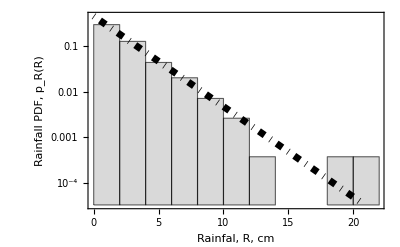

0.638928

0.104281

1.01639

1.20976

USGS site 2485700

2.19037

2.19037

2.19037

0.708406

-0.00491496

```mathematica
site =25;
eventRunoffsite = DeleteCases[eventRunoff[[All,site+1]],""];
eventRainfallsite = DeleteCases[eventRainfall[[All,site+1]],""];
selectedRow=hydroParameters[[site]];
Clear[ω,α1, α2]
params  =
FindDistributionParameters[eventRainfallsite,HyperexponentialDistribution[{ω,1-ω},{1/α1,1/α2}]]
α=α1 ω+α2(1-ω)/.params;
miny = PDF[HyperexponentialDistribution[{ω,1-ω},{1/α1,1/α2}]/.params,Max[eventRainfallsite]];
maxy =  PDF[HyperexponentialDistribution[{ω,1-ω},{1/α1,1/α2}]/.params,0];
prt1 = Histogram[eventRainfallsite,10,"PDF",ScalingFunctions->{"Linear","Log"},PlotRange->{{0,Max[eventRainfallsite]*1.05},{miny ,maxy }},ChartStyle->Directive[LightGray,EdgeForm[Directive[Black]]],PlotTheme->"Detailed"];
prt2=Plot[PDF[HyperexponentialDistribution[{ω,1-ω},{1/α1,1/α2}]/.params,x],{x,0,Max[eventRainfallsite]},PlotStyle->{DotDashed, Black, Thickness[.0125]},PlotRange->{0,2},ScalingFunctions->{"Linear","Log"}] ;
Show[prt1,prt2,Frame->{{True,None},{True,None}},FrameLabel->{"Rainfal, R, cm","Rainfall PDF, p_R(R)"},LabelStyle->{12, Bold}]
EToR=selectedRow["<ET/R>"]
QboQf =selectedRow["<Qb/Qf>"]
σQ2 = selectedRow["sigmaQ^2(cm^2)"]
DI = selectedRow["DI_mean"]
Print["USGS site ",selectedRow["usgs_site_no"]]
α1=α1/.params
α2=α2/.params
ω=ω/.params;
α = α1 ω+α2(1-ω)
(*Avg. Runoff from the data, I don't use the event aggregation because it doesn't capture all the runoff*)
QavgD = α(1-EToR)(1-QboQf)
(*Runoff Additive Adjustment Factor, to adjust the runoff avg to the observations*)
Qf = QavgD -Mean[eventRunoffsite]
eventRunoffsiteScaled = Qf +eventRunoffsite;
```

Calculate the RMSE error in the fit. Note that the rainfall data is in mm and so the RMSE also is in mm.

```mathematica
n=Length[eventRainfallsite];
rainfallSortedData=Sort[eventRainfallsite];
(*Calculate k/(n+1) for each k*)
quantiles=Table[k/(n+1),{k,1,n}];
TheoreticalQuantilesArray={Append[Range[.01,.99,0.01],Max[quantiles*1.0]]};
EmpiricalValuesArray = Table[EmpiricalValues=Table[closestIndex=First[Ordering[Abs[quantiles-q]]];
rainfallSortedData[[closestIndex]],{q,TheoreticalQuantiles}],{TheoreticalQuantiles,TheoreticalQuantilesArray}];
dist = HyperexponentialDistribution[{ω,1-ω},{1/α1,1/α2}]/.params;
TheoreticalValuesArray ={Table[x/.FindRoot[P ==CDF[dist,x],{x,.1}][[1]],{P,Flatten[TheoreticalQuantilesArray]}]};

rmse=Sqrt[Mean[(TheoreticalValuesArray[[1]]-EmpiricalValuesArray[[1]])^2]];
rmse/√Variance[rainfallSortedData]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

0.249429

Compare the fit with a Q-Q plot with the 95-percent confidence band plotted with red dashed lines.

K Statistics is 0.0372397

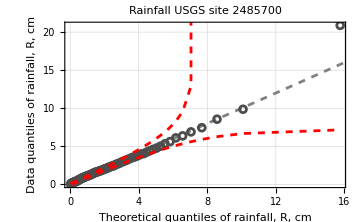

```mathematica
(*Define the confidence level (e.g.,95%)*)
alpha=0.05;
(*Length of Data*)
(*Compute the Kolmogorov-Smirnov statistic for the confidence level*)
kSstatistic=Sqrt[-(1/2) Log[alpha/2]]/Sqrt[n];
Print["K Statistics is ", kSstatistic]

probUpper = (TheoreticalQuantilesArray[[1]]//Flatten)+kSstatistic;(*TheoreticalQuantilesArrayB*)
probLower = (TheoreticalQuantilesArray[[1]]//Flatten)-kSstatistic;(*TheoreticalQuantilesArrayB*)
filteredProbUpper=Select[probUpper,#<=1&];
filteredDataUpper=Pick[(TheoreticalValuesArray[[1]]//Flatten),probUpper,_?(#<=1&)];(*TheoreticalValuesB*)
filteredProbLower=Select[probLower,#>=0&];
filteredDataLower=Pick[(TheoreticalValuesArray[[1]]//Flatten),probLower,_?(#>=0&)];(*TheoreticalValuesB*)
quantilesUpper =Table[(*Print[P];*)x/.FindRoot[P ==CDF[dist,x],{x,.1}][[1]],{P,filteredProbUpper}];
quantilesLower=Table[(*Print[P];*)x/.FindRoot[P ==CDF[dist,x],{x,.1}][[1]],{P,filteredProbLower}];



BandPlot=ListPlot[{Transpose[{Append[filteredDataUpper,filteredDataUpper[[-1]]],Append[quantilesUpper,quantilesUpper[[-1]]*3]}],Transpose[{filteredDataLower,quantilesLower}]},PlotStyle->{{Red,Dashed},{Red,Dashed}}, Joined-> True, PlotRange->All];

linePlot=Plot[x,{x,0,Max[Max[EmpiricalValuesArray[[1]]],Max[Re[TheoreticalValuesArray[[1]]]]]},PlotStyle->{Gray,Dashed},PlotTheme->"Detailed",PlotLegends->None];
quantilePlot=ListPlot[Transpose[{Flatten[TheoreticalValuesArray[[1]]],Flatten[EmpiricalValuesArray[[1]]]}],PlotMarkers->{Graphics[{Thick,Circle[]}],7}, PlotStyle->GrayLevel[.3]];
Show[linePlot,quantilePlot ,BandPlot,PlotRange->{{0,Max[TheoreticalValuesArray[[1]]]},{0,Max[EmpiricalValuesArray[[1]]]}},Frame->{{True,None},{True,None}},FrameLabel->{"Theoretical quantiles of rainfall, R, cm","Data quantiles of rainfall, R, cm"},LabelStyle->{12, Bold},PlotLabel->StringJoin["Rainfall USGS site ",ToString[selectedRow["usgs_site_no"]]],ImageSize->Medium]
```

## Solve for the unknown parameters

In this first part,  we iterate through a list of β value and solves Equations  30-32 of the paper for the three unknown parameters of μ, w, B_I. The left-hand-sides of Eqs. 30-32 are set equal to observations imported into the notebook, which were previously calculated with Python scripts  that extracted the values for each USGS watershed considered here.

For each β, the unknowns are found from the equation solution. In turn, the parameter value are plugged back into the equations to check that they truly are solutions (i.e., the error b/t the left- and right-hand-side of the equations is negligible). Only solution with a negligible error  are carried forward for further analysis.

In some bases, it may be necessary to perturb the initial conditions of FindRoot to converge on an optimal solution.

```mathematica
Clear[ans,μ,β]
betaValues={0.01,.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1};
ansArray=Table[
FindRoot[{EToR ==DI χIavgN1[DI,(w μ)/α]+DI aPET[DI,(w μ)/α]χavgFast[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,ϑ[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],w/α(1-μ),β]],
QboQf == (BI χavgFast[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,ϑ[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],w/α(1-μ),β]])/(1-DI χIavgN1[DI,(w μ)/α]-DI aPET[DI,(w μ)/α] χavgFast[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,ϑ[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],w/α(1-μ),β]]),
σQ2 ==(1-aλ[DI,(w μ)/α])(aλ[DI,(w μ)/α]w(1-μ) qavg[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,ϑ[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],w/α(1-μ),β]])^2+aλ[DI,(w μ)/α]σ2QmFast [(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,w(1-μ) ,ω,w/α1(1-μ),w/α2(1-μ),DI,(w μ)/α]},{{BI,.5,.01,5},{w,10,1,150},{μ,.02,.0001,.85}(*{BI,.3,.01,12},{w,70,5,550},{μ,.01,.0001,.85}*)(*{μ,.01,.001,.75} {β,.1,.01,1}*) },MaxIterations->500,AccuracyGoal->3],{β,betaValues}];
(*New β values*)
(*{BI,5.75,.01,12},{w,70,5,550},{μ,.01,.0001,.85} used as an alternative starting set*)
ansArrayWithBeta = MapThread[Append,{ansArray,β->#&/@betaValues}]
errors=Table[{Abs[EToR -(DI χIavgN1[DI,(w μ)/α]+DI aPET[DI,(w μ)/α]χavgFast[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,ϑ[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],w/α(1-μ),β]])/.ans]+
Abs[QboQf-(BI χavgFast[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,ϑ[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],w/α(1-μ),β]])/(1-DI χIavgN1[DI,(w μ)/α]-DI aPET[DI,(w μ)/α] χavgFast[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,ϑ[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],w/α(1-μ),β]])/.ans]+
Abs[σQ2 -((1-(aλ[DI,(w μ)/α]))(aλ[DI,(w μ)/α]w (1-μ) qavg[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,ϑ[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],w/α(1-μ),β]])^2+aλ[DI,(w μ)/α]σ2QmFast [(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,w(1-μ) ,ω,w/α1(1-μ),w/α2(1-μ),DI,(w μ)/α])/.ans]},{ans,ansArrayWithBeta}];
errors
AcceptablePositions=Position[Flatten[errors],x_/;x<0.001];
SelectedansArrayWithBeta=ansArrayWithBeta[[#]]&/@Flatten[AcceptablePositions]
```

FindRoot::reged: The point {0.34171,11.9453,0.0001} is at the edge of the search region {0.0001,0.85} in coordinate 3 and the computed search direction points outside the region.

FindRoot::reged: The point {0.329528,12.1509,0.0001} is at the edge of the search region {0.0001,0.85} in coordinate 3 and the computed search direction points outside the region.

FindRoot::reged: The point {0.313345,12.4187,0.0001} is at the edge of the search region {0.0001,0.85} in coordinate 3 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

{{BI→0.34171,w→11.9453,μ→0.0001,β→0.01},{BI→0.329528,w→12.1509,μ→0.0001,β→0.1},{BI→0.313345,w→12.4187,μ→0.0001,β→0.2},{BI→0.287489,w→12.803,μ→0.0001,β→0.3},{BI→0.0744792,w→31.4683,μ→0.00415054,β→0.4},{BI→0.0790282,w→31.2047,μ→0.00994037,β→0.5},{BI→0.0822408,w→33.0351,μ→0.013078,β→0.6},{BI→0.0850871,w→36.3647,μ→0.0147546,β→0.7},{BI→0.088545,w→40.2879,μ→0.0163627,β→0.8},{BI→0.0917818,w→46.6449,μ→0.0165046,β→0.9},{BI→0.0919252,w→72.1644,μ→0.0107347,β→1}}

{{0.866122},{0.873752},{0.878569},{0.869902},{2.0937×10^-11},{4.74736×10^-12},{1.92411×10^-11},{1.74803×10^-10},{5.96745×10^-16},{7.55923×10^-14},{1.26186×10^-11}}

{{BI→0.0744792,w→31.4683,μ→0.00415054,β→0.4},{BI→0.0790282,w→31.2047,μ→0.00994037,β→0.5},{BI→0.0822408,w→33.0351,μ→0.013078,β→0.6},{BI→0.0850871,w→36.3647,μ→0.0147546,β→0.7},{BI→0.088545,w→40.2879,μ→0.0163627,β→0.8},{BI→0.0917818,w→46.6449,μ→0.0165046,β→0.9},{BI→0.0919252,w→72.1644,μ→0.0107347,β→1}}

For the previous sets of variables (with negligible error), the code iterates through each set (with an associated β) and calculates the RMSE between the modeled runoff quantiles and the observed quantiles of runoff. In turn, the optimal solution set (based on RMSE) is selected. This could be changed in the future to select an optimal set based on a different metric such as NSE.

```mathematica
n=Length[eventRunoffsiteScaled];
runoffSortedData=Sort[eventRunoffsiteScaled];
(*Calculate k/(n+1) for each k*)
quantiles=Table[k/(n+1),{k,1,n}];
TheoreticalQuantilesArray=Table[
(*Find the closest quantile and corresponding value*)
Append[Range[(1-aλ[DI,(w μ)/α]/.ans),.99,0.01],Max[quantiles*1.0]],{ans,SelectedansArrayWithBeta}];
EmpiricalValuesArray = Table[EmpiricalValues=Table[closestIndex=First[Ordering[Abs[quantiles-q]]];
runoffSortedData[[closestIndex]],{q,TheoreticalQuantiles}],{TheoreticalQuantiles,TheoreticalQuantilesArray}];
(*Add a small value of .0001 to teh initial quantile to avoid zero as the runoff value in the percent bias comparisons*)
TheoreticalValuesArray =Table[Table[(*Print[P];*)Q/.FindRoot[(P-(1-aλ[DI,(w μ)/α]/.ans))/(aλ[DI,(w μ)/α]/.ans)==(*PQm[Q,(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,w(1-μ) ,ω,w/α1(1-μ),w/α2(1-μ)]*)PQmFast[Q,(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,w(1-μ) ,ω,w/α1(1-μ),w/α2(1-μ)]/.ans,{Q,.1,0,∞},AccuracyGoal->2],{P,Evaluate[Append[Range[(1-aλ[DI,(w μ)/α]/.ans),.99,0.01],Max[quantiles*1.0]]]}],{ans,SelectedansArrayWithBeta}];
(*Calculate RMSE*)
Print["RMSE array for the solutions"]
rmseArray=Table[Sqrt[Mean[(TheoreticalValuesArray[[i]]-EmpiricalValuesArray [[i]])^2]],{i, 1, Length[TheoreticalValuesArray]}]
Qavg = Mean[eventRunoffsiteScaled];
Print["NSE array ffor the solutions"]
NSEArray = Table[ 1-Total[(EmpiricalValuesArray [[i]]-TheoreticalValuesArray [[i]])^2]/(Total[(EmpiricalValuesArray [[i]]-Qavg)^2]
),{i, 1, Length[TheoreticalValuesArray]}]
Print["Percent Bias array ffor the solutions"]
PercentBiasArray = Table[Total[(EmpiricalValuesArray [[i]]-TheoreticalValuesArray [[i]])/((*Flatten[EmpiricalValuesArray[[Flatten[posToSelect]]]]*)1)*100]/((*nquantiles*)Total[EmpiricalValuesArray [[i]]]),{i, 1, Length[TheoreticalValuesArray]}]

(*Select value with the smallest RMSE*)
Print["Position in array of optimal solution based on RMSE"]
posToSelect = PositionSmallest[rmseArray]
Print["Optimal solution based on RMSE, RMSE"]
rmseArray[[Flatten[posToSelect]]]//Flatten
Print["Optimal solution parameters"]
SelectedansArrayWithBeta[[Flatten[posToSelect]]]
```

RMSE array for the solutions

{0.141938,0.143758,0.160823,0.173508,0.182219,0.169022,0.219873}

NSE array ffor the solutions

{0.984948,0.986306,0.98293,0.980379,0.979162,0.980604,0.967891}

Percent Bias array ffor the solutions

{-1.78734,-1.87197,-2.97003,-4.4924,-5.22407,-7.38135,-11.0599}

Position in array of optimal solution based on RMSE

{1}

Optimal solution based on RMSE, RMSE

{0.141938}

Optimal solution parameters

{{BI→0.0744792,w→31.4683,μ→0.00415054,β→0.4}}

## Metrics of the Optimal Solution

Here we retrieve metrics of the optimal parameter solution, evaluating the model NSE, NNSE, percent bias, and bias. All of which are for the solution that minimizes the RMSE. This answer would differ if the solution was optimized on a different metric.

```mathematica
Qavg = With[{ans = SelectedansArrayWithBeta[[Flatten[posToSelect]]],α=α*1},aλ[DI,(w μ)/α]w (1-μ) qavg[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,ϑ[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],w/α(1-μ),β]]/.ans][[1]]
Mean[eventRunoffsiteScaled]
nquantiles = Length[Flatten[EmpiricalValuesArray[[Flatten[posToSelect]]]]];
Print["NSE is ",NSE = 1-Total[(Flatten[EmpiricalValuesArray[[Flatten[posToSelect]]]]-Flatten[TheoreticalValuesArray[[Flatten[posToSelect]]]])^2]/(Total[(Flatten[EmpiricalValuesArray[[Flatten[posToSelect]]]]-Qavg)^2]
)]
Print["NNSE is ",NNSE = 1/(2-NSE)]
Print["Percent Bias is ", PercentBias = Total[(Flatten[EmpiricalValuesArray[[Flatten[posToSelect]]]]-Flatten[TheoreticalValuesArray[[Flatten[posToSelect]]]])/((*Flatten[EmpiricalValuesArray[[Flatten[posToSelect]]]]*)1)*100]/((*nquantiles*)Total[Flatten[EmpiricalValuesArray[[Flatten[posToSelect]]]]])]
Print["Bias is ",Bias = 1/nquantiles Total[(Flatten[EmpiricalValuesArray[[Flatten[posToSelect]]]]-Flatten[TheoreticalValuesArray[[Flatten[posToSelect]]]])]]
```

0.708406

0.708406

NSE is 0.984948

NNSE is 0.985171

Percent Bias is -1.78734

Bias is -0.0135946

## Runoff Data vs. Model Comparison Plot

K Statistics is 0.0372397

FindRoot::reged: The point {0.} is at the edge of the search region {0.,∞} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

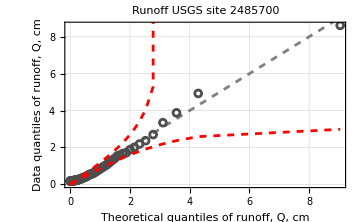

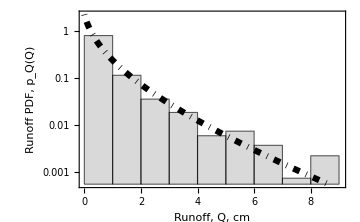

```mathematica
(*Define the confidence level (e.g.,95%)*)
alpha=0.05;
(*Length of Data*)
(*Compute the Kolmogorov-Smirnov statistic for the confidence level*)
kSstatistic=Sqrt[-(1/2) Log[alpha/2]]/Sqrt[n];
Print["K Statistics is ", kSstatistic]

(*TheoreticalQuantilesArrayB=Table[
(*Find the closest quantile and corresponding value*)
(Append[Range[(1-aλ[DI,(w μ)/α]/.ans),.99,0.001],Max[quantiles*1.0]]),{ans,SelectedansArrayWithBeta}];*)
(*TheoreticalValuesB =  With[{ans = SelectedansArrayWithBeta[[Flatten[posToSelect]]]},Table[(*Print[P];*)Q/.FindRoot[(P-(1-aλ[DI,(w μ)/α]/.ans))/(aλ[DI,(w μ)/α]/.ans)==PQm[Q,(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,w(1-μ) ,ω,w/α1(1-μ),w/α2(1-μ)]/.ans,{Q,.1},AccuracyGoal->2],{P,(TheoreticalQuantilesArrayB[[Flatten[posToSelect]]]//Flatten)}]]*)

probUpper = (TheoreticalQuantilesArray[[Flatten[posToSelect]]]//Flatten)+kSstatistic;(*TheoreticalQuantilesArrayB*)
probLower = (TheoreticalQuantilesArray[[Flatten[posToSelect]]]//Flatten)-kSstatistic;(*TheoreticalQuantilesArrayB*)
filteredProbUpper=Select[probUpper,#<=1&];
filteredDataUpper=Pick[(TheoreticalValuesArray[[Flatten[posToSelect]]]//Flatten),probUpper,_?(#<=1&)];(*TheoreticalValuesB*)
filteredProbLower=Select[probLower,#>=0&];
filteredDataLower=Pick[(TheoreticalValuesArray[[Flatten[posToSelect]]]//Flatten),probLower,_?(#>=0&)];(*TheoreticalValuesB*)

quantilesUpper =With[{ans = SelectedansArrayWithBeta[[Flatten[posToSelect]]]},Table[(*Print[P];*)Q/.FindRoot[(P-(1-aλ[DI,(w μ)/α]/.ans))/(aλ[DI,(w μ)/α]/.ans)==PQm[Q,(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,w(1-μ) ,ω,w/α1(1-μ),w/α2(1-μ)]/.ans,{Q,.1,0,∞},AccuracyGoal->2],{P,filteredProbUpper}]];
quantilesLower= With[{ans = SelectedansArrayWithBeta[[Flatten[posToSelect]]]},Table[(*Print[P];*)Q/.FindRoot[(P-(1-aλ[DI,(w μ)/α]/.ans))/(aλ[DI,(w μ)/α]/.ans)==PQm[Q,(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,w(1-μ) ,ω,w/α1(1-μ),w/α2(1-μ)]/.ans,{Q,.1,0,∞},AccuracyGoal->2],{P,filteredProbLower}]];
BandPlot=ListPlot[{Transpose[{Append[filteredDataUpper,filteredDataUpper[[-1]]],Append[quantilesUpper,quantilesUpper[[-1]]*2]}],Transpose[{filteredDataLower,quantilesLower}]},PlotStyle->{{Red,Dashed},{Red,Dashed}}, Joined-> True, PlotRange->All];

linePlot=Plot[x,{x,0,Max[Max[EmpiricalValuesArray[[Flatten[posToSelect]]]],Max[Re[TheoreticalValuesArray[[Flatten[posToSelect]]]]]]},PlotStyle->{Gray,Dashed},PlotTheme->"Detailed",PlotLegends->None];
quantilePlot=ListPlot[Transpose[{Flatten[TheoreticalValuesArray[[Flatten[posToSelect]]]],Flatten[EmpiricalValuesArray[[Flatten[posToSelect]]]]}],PlotMarkers->{Graphics[{Thick,Circle[]}],7}, PlotStyle->GrayLevel[.3]];
Show[linePlot,quantilePlot ,BandPlot,PlotRange->{{0,Max[TheoreticalValuesArray[[Flatten[posToSelect]]]]},{0,Max[EmpiricalValuesArray[[Flatten[posToSelect]]]]}},Frame->{{True,None},{True,None}},FrameLabel->{"Theoretical quantiles of runoff, Q, cm","Data quantiles of runoff, Q, cm"},LabelStyle->{12, Bold},PlotLabel->StringJoin["Runoff USGS site ",ToString[selectedRow["usgs_site_no"]]],ImageSize->Medium]

miny =With[{ans = SelectedansArrayWithBeta[[Flatten[posToSelect]]][[1]]},(aλ[DI,(w μ)/α] 1/(w(1-μ))pqm[Max[eventRunoffsite]/(w(1-μ)),(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β ,ω,w/α1(1-μ),w/α2(1-μ)])/.ans] ;
maxy =  With[{ans = SelectedansArrayWithBeta[[Flatten[posToSelect]]][[1]]},(aλ[DI,(w μ)/α] 1/(w(1-μ))pqm[0/(w(1-μ)),(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β ,ω,w/α1(1-μ),w/α2(1-μ)])/.ans] ;
prt1 = Histogram[eventRunoffsite,10,"PDF",ScalingFunctions->{"Linear","Log"},PlotRange->{{0,Max[eventRunoffsite]*1.05},{miny ,maxy }},ChartStyle->Directive[LightGray,EdgeForm[Directive[Black]]],PlotTheme->"Detailed"];
prt2=With[{ans = SelectedansArrayWithBeta[[Flatten[posToSelect]]][[1]]},Plot[aλ[DI,(w μ)/α](1/(w(1-μ))pqm[Q/(w(1-μ)),(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β ,ω,w/α1(1-μ),w/α2(1-μ)])/.ans,{Q,0,Max[eventRunoffsite]},ScalingFunctions->{"Linear","Log"},PlotStyle->{DotDashed, Black, Thickness[.0125]}]];
Show[prt1,prt2,Frame->{{True,None},{True,None}},FrameLabel->{"Runoff, Q, cm","Runoff PDF, p_Q(Q)"},LabelStyle->{12, Bold}]
```

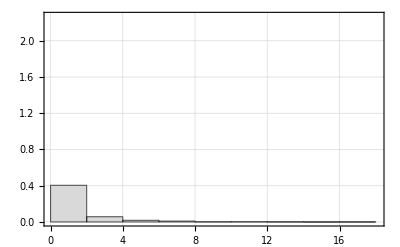

```mathematica
prt1 = Histogram[eventRunoffsite*10*.2,10,"PDF",PlotRange->{{0,Max[eventRunoffsite]*1.05*10*.2},{miny ,maxy }},ChartStyle->Directive[LightGray,EdgeForm[Directive[Black]]],PlotTheme->"Detailed"]
```

## Plot the resulting PDFs of soil moisture for the upper and lower layers

```mathematica
SelectedansArrayWithBeta[[Flatten[posToSelect]]]
```

{{BI→0.0744792,w→31.4683,μ→0.00415054,β→0.4}}

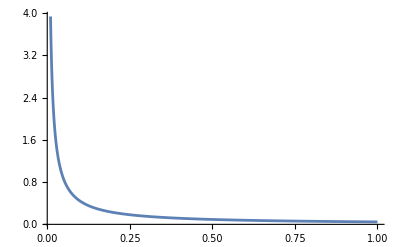

{0.94472}

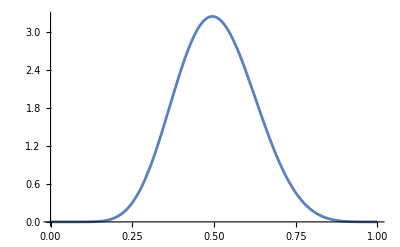

```mathematica
With[{ans = SelectedansArrayWithBeta[[Flatten[posToSelect]]]},Plot[χPDF[x0,DI,(w μ)/α]/.ans,{x0,.01,1},PlotRange->All]]
With[{ans = SelectedansArrayWithBeta[[Flatten[posToSelect]]]},aλ[DI,(w μ)/α]/.ans]
With[{ans = SelectedansArrayWithBeta[[Flatten[posToSelect]]]},Plot[pχPlot[x,(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,ϑ[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],w/α(1-μ),β]]/.ans,{x,0,1},PlotRange->All,PlotPoints->5]]
```

## Plot PDF for specific parameters

{{BI→0.737684,w→537.654,μ→0.00401569,β→0.1}}

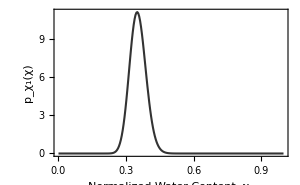

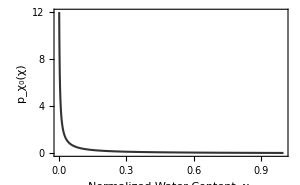

{0.94472}

```mathematica
ansIntput= {{BI->0.7376841879563643,w->537.6543805,μ->0.004015686,β->0.1}}

With[{ans =ansIntput},Plot[pχPlot[x,(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,ϑ[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],w/α(1-μ),β]]/.ans,{x,0,1},PlotRange->All,PlotPoints->5,Frame->True,FrameStyle->{{Directive[ Black],Transparent},{Directive[ Black],Transparent}},FrameLabel->{{"p_χ_1(χ)",""},{"Normalized Water Content, χ_1",""}},PlotStyle->{{Thickness[.005],GrayLevel[.2]}},LabelStyle->Directive[12,Bold],ImageSize->300,PlotRangeClipping->False]]
With[{ans = SelectedansArrayWithBeta[[Flatten[posToSelect]]]},Plot[χPDF[x0,DI,(w μ)/α]/.ans,{x0,0,1},PlotRange->{0,12},Frame->True,FrameStyle->{{Directive[ Black],Transparent},{Directive[ Black],Transparent}},FrameLabel->{{"p_χ_0(χ)",""},{"Normalized Water Content, χ_0",""}},PlotStyle->{{Thickness[.005],GrayLevel[.2]}},LabelStyle->Directive[12,Bold],ImageSize->300,PlotRangeClipping->False]]
With[{ans = SelectedansArrayWithBeta[[Flatten[posToSelect]]]},aλ[DI,(w μ)/α]/.ans]
```

Check that PDF with parameters solution integrates to 1

```mathematica
With[{ans =ansIntput},NIntegrate[pχ[x,(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],(w (1-μ))/α,β,ϑ[(DI aPET[DI,(w μ)/α]+BI)/aλ[DI,(w μ)/α],w/α(1-μ),β]]/.ans,{x,0,1}]]
```